## Introduction

### Background

```mathematica
Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\material.jpg"]
```

-Graphics-

In this material, the magnetic domains are perpendicular to each-other, in and out of the surface. When an external magnetic field is applied to the material, more of the domains in the material align with that field. A Magnetic Force Microscope can image those domains

```mathematica
Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\domains.jpg"]
```

-Graphics-

Magnetic Image Examples:
Here are four images of the same location on the same material. The only difference between the images is the applied filed, which is 0.25T, 0.30T, 0.35T, 0.40T respectively from top to bottom. The images are 2µm squares. 

(Explain what is happening as field is increased.)

```mathematica
Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\25T.jpg"]
Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\30T.jpg"]
Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\35T.jpg"]
Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\40T.jpg"]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Problem

There is a definite morphology in the magnetic domains as the applied field increases. For my project, I was looking for a way to quantify the change so that we could see a what kind of trend an increasing field has. This would give numerical verification to my observations.

## Final Project

### Method One

This method takes a grayscale image and converts it to a binary image. The white pixels have a value of one and the black pixels zero. I can then sum all of the pixel values and get a ratio of the pixel values to the total number of pixels. This ratio can be compared across images to give an indication of the trend in the changing domains

#### Function 1 - change pixel from gray to black of white

```mathematica
(*this function takes a single gray pixel and converts it to black or white, pivoting around .5*)
blackorwhite[pixel_]:=Module[{pVal,myPixel},
myPixel=pixel;
pVal = Total[myPixel];
If[pVal >= .5, myPixel =1, myPixel = 0]; 
(*it should be noted that the value of .5 as the pivot is arbitray, as I am just concerned with the change across images*)
myPixel
]

(*this function can be applied to each pixel of a grayscale image using the Map function*)
```

#### Function 2- take a binary image and return ratio of black to white pixels

```mathematica
binaryratio[binarydata_]:=Module[{rows,columns,numpixels, pixeltotal,imagesize,ratio},
imagesize=Dimensions[binarydata];
rows=imagesize[[1]];
columns=imagesize[[2]];
pixeltotal=Total[binarydata,2];
numpixels=rows*columns;
ratio=pixeltotal/numpixels//N
]

(*it would be useful to plot these ratios taken from different images to the trend*)
```

### Method Two

This method is involves only one function. It takes a grayscale image and totals the individual pixel values. This method may return a more accurate representation of what is happening physically, that being, it may be closer to the actual ratio of magnetic domains pointing out of the surface of a material to the total domains.

#### Function 1

```mathematica
findthreshold[data_]:=Module[{rows,columns,numpixels, pixeltotal,imagesize,threshhold},
imagesize=Dimensions[data];
rows=imagesize[[1]];
columns=imagesize[[2]];
pixeltotal=Total[data,2];
numpixels=rows*columns;
threshhold=pixeltotal/numpixels
]

(*If you take the first function from the first method and change the pivot to be the threshhold, the resulting image is a the best binary representation of the the original image*)
```

### Get Test Images/Convert to Grayscale

```mathematica
colorImage1=Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\25T.jpg"]
image1=ColorConvert[colorImage1,"Grayscale"]
```

-Graphics-

-Graphics-

```mathematica
colorImage2=Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\30T.jpg"]
image2=ColorConvert[colorImage2,"Grayscale"]
```

-Graphics-

-Graphics-

```mathematica
colorImage3=Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\35T.jpg"]
image3=ColorConvert[colorImage3,"Grayscale"]
```

-Graphics-

-Graphics-

```mathematica
colorImage4=Import["C:\\Users\\mttri\\Desktop\\PHYSC 230\\230FinalProject\\40T.jpg"]
image4=ColorConvert[colorImage4,"Grayscale"]
```

-Graphics-

-Graphics-

### Method One Test

#### Image One Method One

```mathematica
binary1M1=Map[blackorwhite,ImageData[image1],{2}];
Image[binary1M1]
(*.25T*)
```

-Graphics-

```mathematica
I1M1=binaryratio[binary1M1]
```

0.224336

#### Image Two Method One

```mathematica
binary2M1=Map[blackorwhite,ImageData[image2],{2}];
Image[binary2M1]
(*.30T*)
```

-Graphics-

```mathematica
I2M1=binaryratio[binary2M1]
```

0.257699

#### Image Three Method One

```mathematica
binary3M1=Map[blackorwhite,ImageData[image3],{2}];
Image[binary3M1]
(*.35T*)
```

-Graphics-

```mathematica
I3M1=binaryratio[binary3M1]
```

0.255991

#### Image Four Method One

```mathematica
binary4M1=Map[blackorwhite,ImageData[image4],{2}];
Image[binary4M1]
(*.40T*)
```

-Graphics-

```mathematica
I4M1=binaryratio[binary4M1]
```

0.246715

#### Plot

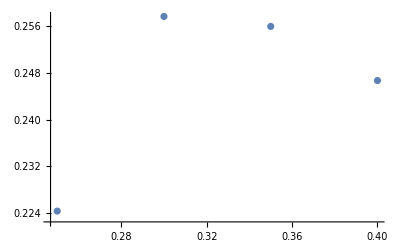

```mathematica
ListPlot[{{.25,I1M1},{.30,I2M1},{.35,I3M1},{.40,I4M1}}]
```

### Method Two Test

#### Image One Method Two

```mathematica
I1M2=findthreshold[ImageData[image1]]
```

0.367732

#### Image One made Binary

```mathematica
blackorwhite1[pixel_]:=Module[{myPixel},
myPixel=pixel;
If[myPixel ≥I1M2, myPixel =1, myPixel = 0];
myPixel
]


binary1M2=Map[blackorwhite1,ImageData[image1],{2}];
Image[binary1M2]
```

-Graphics-

#### Image Two Method Two

```mathematica
I2M2=findthreshold[ImageData[image2]]
```

0.365697

#### Image Two Made Binary

```mathematica
blackorwhite2[pixel_]:=Module[{pVal,myPixel},
myPixel=pixel;
pVal = Total[myPixel];
If[pVal >= I2M2, myPixel =1, myPixel = 0];
myPixel
]




binary2M2=Map[blackorwhite2,ImageData[image1],{2}];
Image[binary2M2]
```

-Graphics-

#### Image Three Method Two

```mathematica
I3M2=findthreshold[ImageData[image3]]
```

0.365591

#### Image Three Made Binary

```mathematica
blackorwhite3[pixel_]:=Module[{pVal,myPixel},
myPixel=pixel;
pVal = Total[myPixel];
If[pVal >= I3M2, myPixel =1, myPixel = 0];
myPixel
]


binary3M2=Map[blackorwhite1,ImageData[image3],{2}];
Image[binary3M2]
```

-Graphics-

#### Image Four Method Two

```mathematica
I4M2=findthreshold[ImageData[image4]]
```

0.366713

#### Image Four Made Binary

```mathematica
blackorwhite4[pixel_]:=Module[{pVal,myPixel},
myPixel=pixel;
pVal = Total[myPixel];
If[pVal >= I4M2, myPixel =1, myPixel = 0];
myPixel
]





binary4M2=Map[blackorwhite1,ImageData[image1],{2}];
Image[binary4M2]
```

-Graphics-

### Plots

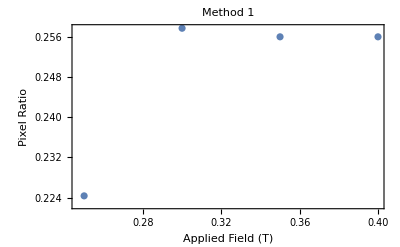

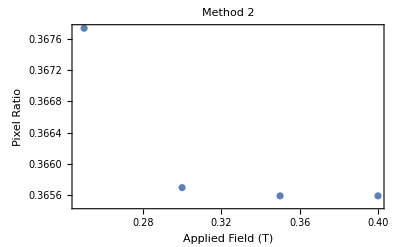

```mathematica
ListPlot[{{.25,I1M1},{.30,I2M1},{.35,I3M1},{.40,I3M1}},PlotLabel->"Method 1",FrameLabel->{"Applied Field (T)","Pixel Ratio"},Frame->True]
ListPlot[{{.25,I1M2},{.30,I2M2},{.35,I3M2},{.40,I3M2}},PlotLabel->"Method 2",FrameLabel->{"Applied Field (T)","Pixel Ratio"},Frame->True]
```